
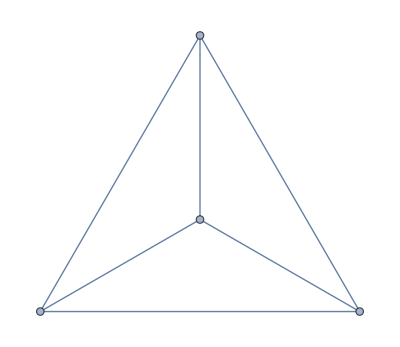
-Graphics-→-Graphics-

```mathematica
CompleteGraph[3]->CompleteGraph[4]
```

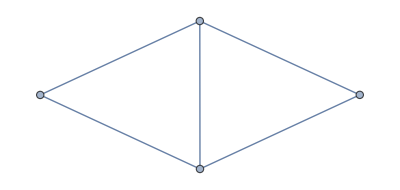
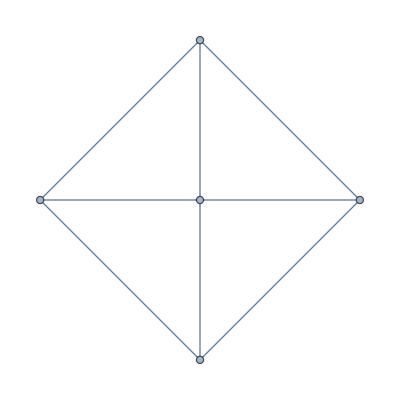
-Graphics-→-Graphics-

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->1,1<->3}]->WheelGraph[5]
```

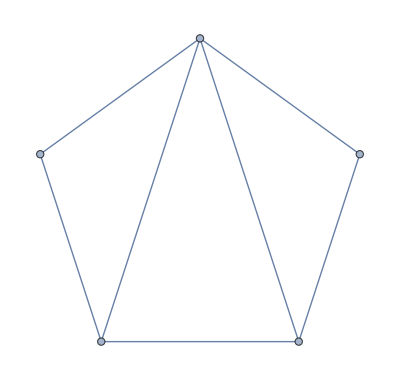
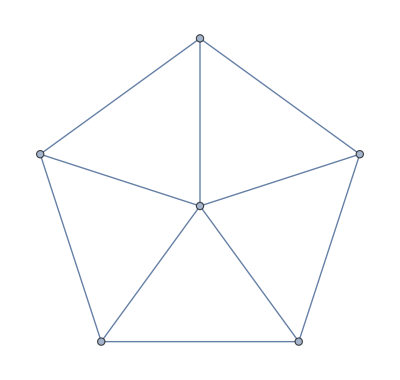
-Graphics-→-Graphics-

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->3,1<->4},GraphLayout->"TutteEmbedding"]->WheelGraph[6]
```

```mathematica
all4=Get["d:\\Saved\\complete4.m"]
```

<|0→<|signature→0,12,colortable→{{v1234+v123x4+v124x3+v12x34+v12x3x4,v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v134x2+v13x24+v13x2x4,v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v134x2+v14x23+v14x2x3,v123x4+v12x34+v12x3x4+4+v1x24x3+v1x2x34+v1x2x3x4},{1},{v1234+v124x3+v13x24+v1x234+v1x24x3,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4},{v1234+v12x34+v134x2+v1x234+v1x2x34,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4}}|>,125,2→<|1|>|>
 |  |  |  |

```mathematica
Table[all4[k,"graph"],{k,Keys[all4]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[Keys[all4]]
```

127

```mathematica
Table[all4[k,"graph"],{k,Select[Keys[all4],Length[ListofVars[all4[#,"colofour"]]]==1&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[allGraphs[k,"graph"],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofournull"]]]==1&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[allGraphs[k,"graph"],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]≠"Greater"&]
```

{364,367,445,448}

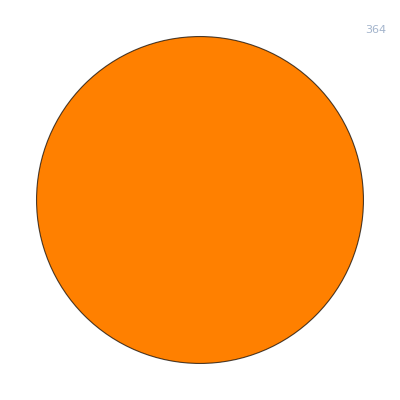
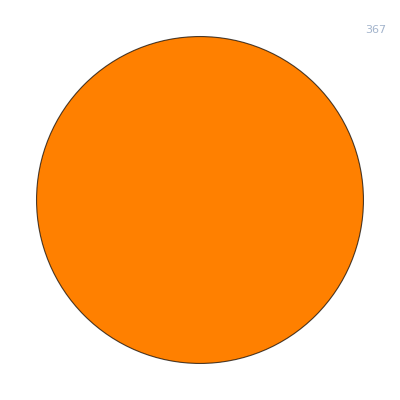
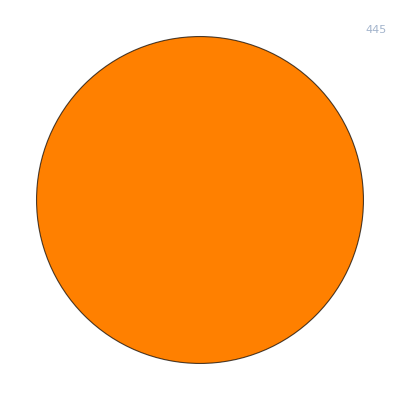
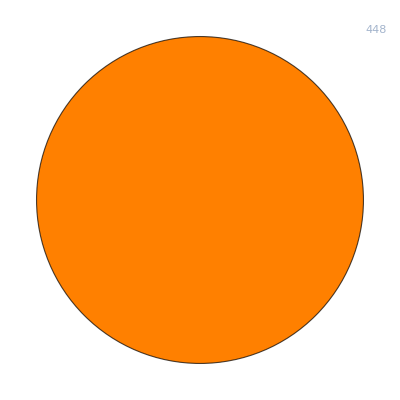

```mathematica
Table[DependencyGraph[ allGraphs,k],{k,Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]≠"Greater"&]}]
```

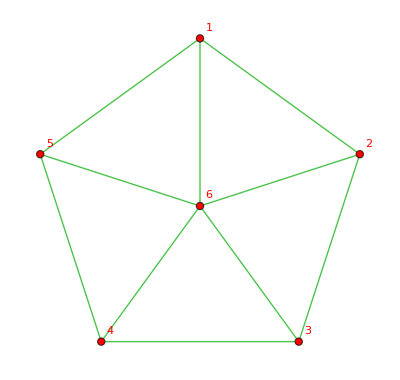
-Graphics-==-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
WheelGraph[6,VertexStyle->Red,EdgeStyle->Darker[Green],VertexLabels->{1->6,5->1,4->2,3->3,2->4,6->5}]==Total[Table[allGraphs[k,"graph"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]
```

```mathematica
Select[Keys[allGraphs],ToString[allGraphs[#,"comp"]]=="Greater"&& Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==2 &]
```

{19683,29888,30586,29097,32684,31194,27519,28218,26730,26732,33048,37521,39014,34539,33050,22817,23518,22032,22038,24138,25625,24144,20466,20484,21168,21186,19701,19709,19689,19685,46170,49220,49972,48456,50715,52232,46932,47685,46172,55251,56012,56770,58288,53733,52975,41634,42392,43147,41640,44659,43905,40122,40140,40887,39375,39380,39382,39388,39369,39367,6561,9503,10228,8820,8766,10944,12407,10998,7458,7296,8022,8184,6723,6779,6615,6563,15318,16052,16783,15372,18247,17541,13854,14016,14667,13203,13232,13258,13312,13149,13123,2187,3404,2918,3646,4132,2673,2733,2241,2193,5104,5590,6077,4617,4650,4674,4890,4401,4377,729,1215,1395,891,747,1701,1800,1872,2034,1539,1467,243,377,400,342,414,473,276,300,245,576,608,637,697,516,487,81,110,136,87,190,165,27,45,63,9,14,16,22,3,1}

```mathematica
allGraphs[19683,"graph"]
```

-Graphics-

```mathematica
allGraphs[19683,"graph"]==allGraphs[19683,"colofourrealnull"]/.repcolofourrealnullgraph2
```

-Graphics-==--Graphics-n12x3x4x539366+-Graphics-n1x2x3x4x50

```mathematica
Simplify[allGraphs[19683,"colofourrealnull"]>0]/.repcolofourrealnullgraph2
```

-Graphics-n1x2x3x4x50>-Graphics-n12x3x4x539366

```mathematica
Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==6]&]
```

{364}

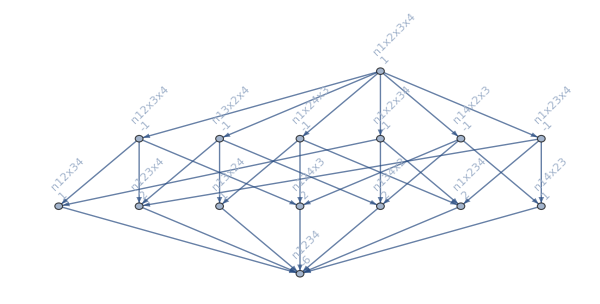

```mathematica
Graph[MobiusGraph[364],DirectedEdges->False]
```

```mathematica
allGraphs[364,"graph"]
```

-Graphics-

```mathematica
ChromaticPolynomial[allGraphs[364,"graph"],x]//TraditionalForm
```

x^4-6 x^3+11 x^2-6 x

```mathematica
allGraphs[alfa1Key,"colofourrealnull"]/.repcolofourrealnullgraph2/."-" ->Style["-",Red]
```

2 -Graphics-n1234559048--Graphics-n1234x557528--Graphics-n135x2414748--Graphics-n13x24513340+-Graphics-n13x24x513284

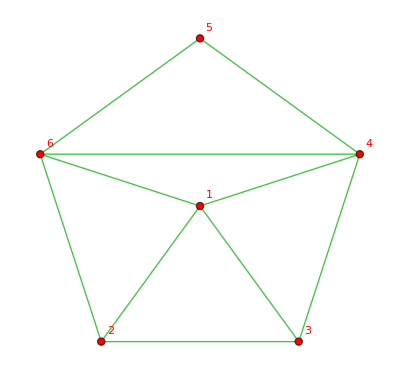

```mathematica
EdgeAdd[EdgeDelete[WheelGraph[6, VertexLabels->"Name",VertexStyle->Red,EdgeStyle->Darker[Green],VertexLabels->{1->6,5->1,4->2,3->3,2->4,6->5}],1<->5],4<->6]
```

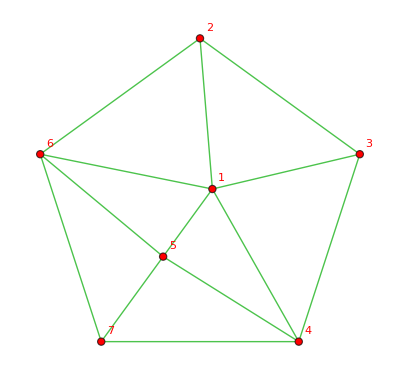

```mathematica
Graph[EdgeAdd[WheelGraph[6, VertexLabels->"Name",VertexStyle->Red,EdgeStyle->Darker[Green],VertexLabels->{1->6,5->1,4->2,3->3,2->4,6->5}],{6<->7,5<->7,4<->7}],GraphLayout->"TutteEmbedding"]
```

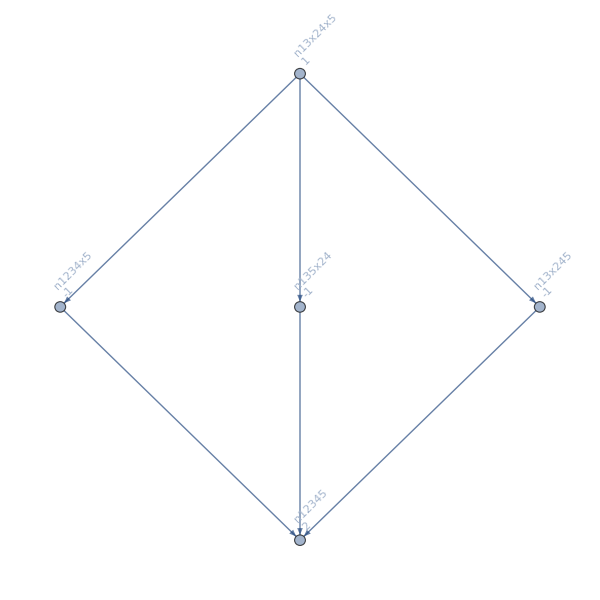

```mathematica
Graph[MobiusGraph[alfa1Key],DirectedEdges->False]
```

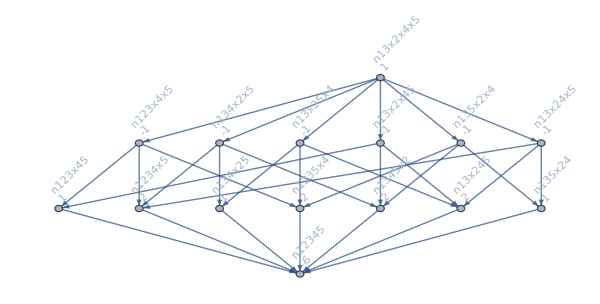

```mathematica
Graph[MobiusGraph[quad1Key],DirectedEdges->False]
```